```mathematica
OverleafPath = "/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)"
```

/Users/yorickreum/Dropbox/Apps/Overleaf/BA Thesis (MIT Template)

```mathematica
lossesData = Import["/Users/yorickreum/PycharmProjects/pytorch_pde/approximator/examples/heat/hyperstudy/trials/2021-03-13 05:53:28.260384/losses.csv", "Table"]
```

{{0.563681237963143067},{0.515719382271826787},{0.475928205032757179},549061,{1.12141282056970239×10^-6},{1.03017225243221829×10^-6},{9.09020143275859585×10^-7}}
 |  |  |  |

```mathematica
LossInterpolation = Interpolation[lossesData]
```

InterpolatingFunction[{{1.000000000000000000, 549067.000000000000}}, <>]

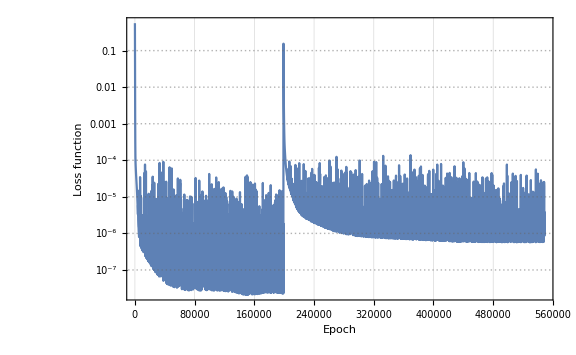

```mathematica
Plot[
LossInterpolation[x],
Flatten@Join[{x},LossInterpolation["Domain"]],
ScalingFunctions->"Log",
PlotTheme->"Detailed",
PlotRange->Full,
PlotRangePadding->{{Scaled[.01], Scaled[.01]},{Scaled[.01], Scaled[.01]}},
ImageSize->Large,
PlotLegends->None,
FrameStyle->Black,
FrameLabel->{"Epoch","Loss function"}
]
```